### Options

```mathematica
SetOptions[EvaluationNotebook[],DynamicUpdating->False]
```

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False];
```

```mathematica
$Version
```

14.0.0 for Microsoft Windows (64-bit) (December 13, 2023)

### Functions

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False];
```

```mathematica
Clear[traitAbundDist];
traitAbundDist[l_,t_,nt_,nc_,b0_,r_,ni_]:= traitAbundDist[l,t,nt,nc,b0,r,ni] =
-(b0 nc nt^2 r^2 ((l (-1+nc) (-b0+t))/(nc nt r^2 t))^ni Pochhammer[(2-2 nc+nt (-1+(√(b0+4 b0 (-1+nc) nc r^2-t))/(√(b0-t))))/(2-2 nc),-1+ni] Pochhammer[(-2+2 nc+nt+(nt √(b0+4 b0 (-1+nc) nc r^2-t))/(√(b0-t)))/(2 (-1+nc)),-1+ni])/((-1+nc) (b0-t) Gamma[1+ni])
```

```mathematica
indivRepertoire [l_,t_,nt_,nc_,b0_,r_]:= IndivRepertoire [l,t,nt,nc,b0,r] = (*why is this so slow compared to just writing the equations?*)
Sum[( traitAbundDist [l,t,nt,nc,b0,r,ni]/ Sum[ traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}]) (1-(1-(ni (1+((-1+nc) ni)/nt))/(nc nt r^2))^l)  t, {ni,0,nt}]
```

```mathematica
Clear[popRepertoire];
popRepertoire [l_,t_,nt_,nc_,b0_]:= popRepertoire[l,t,nt,nc,b0]=

z=r/. FindRoot[r==Sum[ ( traitAbundDist [l,t,nt,nc,b0,r,ni]/ Sum[ traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}]) (1-(1-(ni (1+((-1+nc) ni)/nt))/(nc nt r^2))^l)  t, {ni,0,nt}],{r,0.8,10}, Method->"Brent"];
```

### The average probability of social learning of a focal trait by a newborn (Binomial)

nc: the total number of connections the focal individual has
q: the probability of an an individual having the focal trait
r: the average repertoire size

Assumptions:
1- the sum of repertoire size of N individuals is rN (this assumption is more accurate when N is large)

```mathematica
Sum[x/(nc r) (1-q)^(nc-x)q^x Binomial[nc,x],{x,0,nc}]
```

q/r

The average learning of a trait

```mathematica
FullSimplify[Sum[(x/(nc r))^2 (1-q)^(nc-x)q^x  Binomial[nc,x],{x,0,nc}], {nc>0, 1>q>0}]
```

(q (1+(-1+nc) q))/(nc r^2)

```mathematica
FullSimplify[Sum[(x/(nc r))^2 (1-q)^(nc-x)q^x  Binomial[nc,x],{x,0,nc}], {nc>0, 1>q>0}]
```

```mathematica
(*Manipulate[Plot[{(q (1+(-1+nc) q))/(nc r^2),q^2/r^2},{q,0,1}, PlotRange->{0,1},AxesLabel->{"social learning probability", "trait relative frequency(q)"}],
{{nc,5},1,20},{{r,3},1,10}]
```

#### The average probability of social learning of a focal trait by a newborn (Hypergeometric)

Conclusion: Binomial approximates it very closely. But does it become problematic when thinking about multiple traits?

```mathematica
FullSimplify[Sum[(x/(nc r))^2  ((Binomial[q nt, x]Binomial[(1-q)nt,nc-x])/Binomial[nt,nc]),{x,0,nc}], {nt>1,nc>0, 1>q>0}]
```

(q (-nc+nt+(-1+nc) nt q))/(nc (-1+nt) r^2)

```mathematica
Manipulate[Plot[{(q (1+(-1+nc) q))/(nc r^2),(q (-nc+nt+(-1+nc) nt q))/(nc (-1+nt) r^2)},{q,0,1}, PlotRange->Full,AxesLabel->{"trait relative frequency(q)","social learning probability"}],
{{nc,5},1,20},{{nt,100},6,200},{{r,3},1,10}]
```

#### The effect of the correlation between the number of individuals who have the trait and the repertoire size (rqcor)

```mathematica
FullSimplify[Sum[(x/(nc (r+rqcor q)))^2 (1-q)^(nc-x)q^x  Binomial[nc,x],{x,0,nc}], {nc>0, 1>q>0}] (*rqcor is the correlation between r and q. it is non-zero if being among individuals who have the trait increases their expected average repertoire size. It is important when the repertoire size is small for example. I think it shoul be fine to ignore this*)
```

(q (1+(-1+nc) q))/(nc (r+q rqcor)^2)

```mathematica
Manipulate[Plot[{(q (1+(-1+nc) q))/(nc r^2),(q (1+(-1+nc) q))/(nc (r+q rqcor)^2)},{q,0,1},PlotLegends->{"constant r","r increases with q"}, PlotRange->Full,AxesLabel->{"trait relative frequency(q)","social learning probability"}],
{{nc,5},1,20},{{nt,100},6,200},{{r,3},1,10}, {{rqcor,.1},0,1}]
```

### Neutral theory and relative species abundance in ecology (2003) (not solved)

I'm trying to replicate the results of Volkov et al. (2003)

```mathematica
bn = (1-m)n/J (J-n)/(J-1)+m μk/Jm(1-n/J)
```

((1-m) (J-n) n)/((-1+J) J)+(m (1-n/J) μk)/Jm

```mathematica
dn = (1-m)n/J (J-n)/(J-1)+m(1-μk/Jm) n/J
```

((1-m) (J-n) n)/((-1+J) J)+(m n (1-μk/Jm))/J

```mathematica
dn/.n-> n+1
```

((1-m) (-1+J-n) (1+n))/((-1+J) J)+(m (1+n) (1-μk/Jm))/J

```mathematica
Product[bn/(dn/.n-> n+1), {n,0,n-1}]
```

(J m μk Pochhammer[1-J,-1+n] Pochhammer[1-((-1+J) m μk)/(Jm (-1+m)),-1+n])/((Jm-m μk) Gamma[1+n] Pochhammer[(Jm (-2+J+m)-(-1+J) m μk)/(Jm (-1+m)),-1+n])

```mathematica
FullSimplify[Sum[(J m μk Pochhammer[1-J,-1+n] Pochhammer[1-((-1+J) m μk)/(Jm (-1+m)),-1+n])/((Jm-m μk) Gamma[1+n] Pochhammer[(Jm (-2+J+m)-(-1+J) m μk)/(Jm (-1+m)),-1+n]),n], {J>0, 1>m>0,μk>0, Jm>0}]
```

-1+Hypergeometric2F1[-J,-((-1+J) m μk)/(Jm (-1+m)),((-1+J) (Jm-m μk))/(Jm (-1+m)),1]-(m μk Gamma[-J+n] Gamma[(Jm (-2+J+m)-(-1+J) m μk)/(Jm (-1+m))] Gamma[n-((-1+J) m μk)/(Jm (-1+m))] HypergeometricPFQRegularized[{1,-J+n,n-((-1+J) m μk)/(Jm (-1+m))},{1+n,(Jm (-1+J+(-1+m) n)-(-1+J) m μk)/(Jm (-1+m))},1])/((-Jm+m μk) Gamma[-J] Gamma[1-((-1+J) m μk)/(Jm (-1+m))])

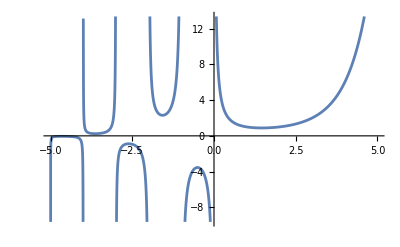

```mathematica
Plot [Gamma[n],{n,-5,5}]
```

```mathematica
Manipulate[Plot[Pochhammer[1-J,n],{n,0,100}, PlotRange->{-50,50}],
{J,-1,100}]
```

```mathematica
Manipulate[Plot[Log[(J m P0 μk Pochhammer[1-J,-1+n] Pochhammer[1-((-1+J) m μk)/(Jm (-1+m)),-1+n])/((Jm-m μk) Gamma[1+n] Pochhammer[(Jm (-2+J+m)-(-1+J) m μk)/(Jm (-1+m)),-1+n])],{n,0,100}],
{{J,100},1,1000},{m,0,1},{{μk,100},1, 1000},{{Jm,1000},1, 10000}, {{P0,50},0,100}]
```

### Distribution of trait abundance in random network (v2)

b0: probability of trait innovation
nt: total number of individuals
dn: Probability of having the trait by the individual who is dying = n/N
bn: probability of acquiring trait by the newly born individual
ni: number of individuals who have the trait
q = ni/nt
p: probability of being connected to someone (connections are random) 
r: average repertoire size
t : number of traits

```mathematica
Clear[b0,nt,dn,bn,ni,l, nc,q,p,r,t]
```

```mathematica
bn = l(b0/t + (1-b0/t)(q (1+(-1+nc) q))/(nc r^2))/. q-> ni/nt // Simplify (*linear approximation// the most inaccurate*)(* here we plug in the average value for q. I'm not sure if it's a good idea. As Erol said, individuals are not experiencing the average necessarily when the trait is rare and it's not meaningful to think about average.*)
(*This is assuming that the trait won't be learnt twice in the successive rounds of learning, which is only accurate for rare traits but overestimates the probability of learning of more common traits and I don't know what to do about it. ASK EROL*)
```

(l (b0-(ni ((-1+nc) ni+nt) (b0-t))/(nc nt^2 r^2)))/t

```mathematica
bn2 = 1-Exp[-l(b0/t + (1-b0/t)(q (1+(-1+nc) q))/(nc r^2))]/. q-> ni/nt (*exponential approximation // not solvable*)
```

1-ⅇ^(-l ((ni (1+((-1+nc) ni)/nt) (1-b0/t))/(nc nt r^2)+b0/t))

```mathematica
bn3 =  1- (1-(b0/t + (1-b0/t)(q (1+(-1+nc) q))/(nc r^2)))^l/. q-> ni/nt (*exact calculation // not solvable*)
```

1-(1-(ni (1+((-1+nc) ni)/nt) (1-b0/t))/(nc nt r^2)-b0/t)^l

```mathematica
bn4 = 1/(1+1/x)/.x->l(b0/t + (1-b0/t)(q (1+(-1+nc) q))/(nc r^2))/. q-> ni/nt (*hyperbolic approximation // solvable*)
```

1/(1+1/(l ((ni (1+((-1+nc) ni)/nt) (1-b0/t))/(nc nt r^2)+b0/t)))

```mathematica
bn5 = 1-Exp[-l(b0/t + (q (1+(-1+nc) q))/(nc r^2))]/. q-> ni/nt  (*simplified exponential approximation // not solvable*)
```

```mathematica
bn6 = 1-Exp[-l(b0/t + q^2/r^2)]/. q-> ni/nt (*more simplified expoential approximation // not solvable*)
```

1-ⅇ^(-l (ni^2/(nt^2 r^2)+b0/t))

```mathematica
Manipulate[Plot[{(l (b0-(ni ((-1+nc) ni+nt) (b0-t))/(nc nt^2 r^2)))/t,1-ⅇ^(-l ((ni (1+((-1+nc) ni)/nt) (1-b0/t))/(nc nt r^2)+b0/t)), 1-(1-(ni (1+((-1+nc) ni)/nt) (1-b0/t))/(nc nt r^2)-b0/t)^l, 1/(1+1/(l ((ni (1+((-1+nc) ni)/nt) (1-b0/t))/(nc nt r^2)+b0/t)))}(*/. { ni-> 10, t -> 100, nt -> 50, r -> 5, b0->0.3, nc->3}*),{l,1,1000},PlotLegends->{"linear approximation","exponential approximation", "exact", "hyperbolic approximation"}, AxesLabel->{"rounds of learning (l)", "probability of learning"}, PlotRange->{0,1}],
{{nc,5},1,20},{{nt,100},6,200},{{ni,10},6,200},{{r,3},1,10},{{b0,0.001},0,0.1},{{t,100},6,200}]
```

```mathematica
dn = ni/nt
```

ni/nt

```mathematica
FullSimplify[Product [(bn4/.ni->ndum)/(dn/.ni-> ndum+1),{ndum,0,ni-1}],{b0>0, t>0, l>0, nt>0, nc>0,nt>nc, r>0}]
```

(b0 l nt^ni Pochhammer[(2-2 nc+nt (-1+(√(b0+4 b0 (-1+nc) nc r^2-t))/(√(b0-t))))/(2-2 nc),-1+ni] Pochhammer[(-2+2 nc+nt+(nt √(b0+4 b0 (-1+nc) nc r^2-t))/(√(b0-t)))/(2 (-1+nc)),-1+ni])/((b0 l+t) Gamma[1+ni] Pochhammer[(-2+2 nc+nt-(nt √(b0 l+4 b0 l (-1+nc) nc r^2-l t+4 (-1+nc) nc r^2 t))/(√(l (b0-t))))/(2 (-1+nc)),-1+ni] Pochhammer[(-2+2 nc+nt+(nt √(b0 l+4 b0 l (-1+nc) nc r^2-l t+4 (-1+nc) nc r^2 t))/(√(l (b0-t))))/(2 (-1+nc)),-1+ni])

```mathematica
Clear[traitAbundDist];
traitAbundDist[l_,t_,nt_,nc_,b0_,r_,ni_]:= traitAbundDist[l,t,nt,nc,b0,r,ni] =
(b0 l nt^ni Pochhammer[(2-2 nc+nt (-1+(√(b0+4 b0 (-1+nc) nc r^2-t))/(√(b0-t))))/(2-2 nc),-1+ni] Pochhammer[(-2+2 nc+nt+(nt √(b0+4 b0 (-1+nc) nc r^2-t))/(√(b0-t)))/(2 (-1+nc)),-1+ni])/((b0 l+t) Gamma[1+ni] Pochhammer[(-2+2 nc+nt-(nt √(b0 l+4 b0 l (-1+nc) nc r^2-l t+4 (-1+nc) nc r^2 t))/(√(l (b0-t))))/(2 (-1+nc)),-1+ni] Pochhammer[(-2+2 nc+nt+(nt √(b0 l+4 b0 l (-1+nc) nc r^2-l t+4 (-1+nc) nc r^2 t))/(√(l (b0-t))))/(2 (-1+nc)),-1+ni])//Re
```

```mathematica
traitAbundDist [l,t,nt,nc,b0,r,ni]/.  {l->1000, t -> 100, nt -> 100, r -> 6, b0->0.01, nc->5, ni ->66}
```

2.24401×10^27+0. ⅈ

```mathematica
l=1000; t = 100; nt = 100; r = 6; b0=0.01; nc=5;
Table[{ni,SetPrecision[ traitAbundDist [l,t,nt,nc,b0,r,ni],50]},{ni,0,nt}]
Clear[l,t,nt,r,b0,nc]
```

{{0,1.0000000000000004440892098500626161694526672363281},{1,9.090909090909089940168996690772473812103271484375},{2,61.94185509283817481218648026697337627410888671875},{3,372.3114439968068154485081322491168975830078125},{4,2073.65050112378639823873527348041534423828125},{5,10927.660045104506934876553714275360107421875},{6,55058.897852784735732711851596832275390625},{7,266791.0356706875027157366275787353515625},{8,1.2476190578853897750377655029296875×10^6},{9,5.643313720639110542833805084228515625×10^6},{10,2.47279163291940651834011077880859375×10^7},{11,1.0507870926294560730457305908203125×10^8},{12,4.33385794214050948619842529296875×10^8},{13,1.7360238500128619670867919921875×10^9},{14,6.75774831840323543548583984375×10^9},{15,2.557585494313232421875×10^10},{16,9.41540854237661895751953125×10^10},{17,3.3730055169320172119140625×10^11},{18,1.176372365652939453125×10^12},{19,3.99575578712314404296875×10^12},{20,1.322369610620053125×10^13},{21,4.26557736194960234375×10^13},{22,1.3416625562455165625×10^14},{23,4.11639624197692×10^14},{24,1.23243990493109775×10^15},{25,3.602082801250528×10^15},{26,1.028120146862906×10^16},{27,2.866798929674072×10^16},{28,7.8121873603353568×10^16},{29,2.08126201621678944×10^17},{30,5.42267821432316992×10^17},{31,1.382247063801106176×10^18},{32,3.44819253772320256×10^18},{33,8.421275884490205184×10^18},{34,2.0141355144115666944×10^19},{35,4.7191628913012334592×10^19},{36,1.08354019846114394112×10^20},{37,2.43873350738576572416×10^20},{38,5.38214734658452258816×10^20},{39,1.1650608109381844992×10^21},{40,2.474403013885342253056×10^21},{41,5.157573130729191112704×10^21},{42,1.0553463549773284900864×10^22},{43,2.120499300057063882752×10^22},{44,4.1849562655264587382784×10^22},{45,8.1145966314588850880512×10^22},{46,1.54624086852691120095232×10^23},{47,2.89620974922574141063168×10^23},{48,5.33373588666724554637312×10^23},{49,9.66017950146058315104256×10^23},{50,1.721045203772338071404544×10^24},{51,3.01683555101214322458624×10^24},{52,5.204271070386029284294656×10^24},{53,8.837135766066099667337216×10^24},{54,1.4774023342510340615176192×10^25},{55,2.43227048814995197394944×10^25},{56,3.944018651323301065916416×10^25},{57,6.300372570337804399149056×10^25},{58,9.9169457741938149728190464×10^25},{59,1.53835459536683962858471424×10^26},{60,2.3522437430720786035900416×10^26},{61,3.545963920705720367972352×10^26},{62,5.27095686405175641473286144×10^26},{63,7.72721730530282308288643072×10^26},{64,1.117400911452677372406398976×10^27},{65,1.59411363038683285371748352×10^27},{66,2.244008335428055827046465536×10^27},{67,3.117406025791404642410692608×10^27},{68,2.212226690957697258633560064×10^27},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0},{88,0},{89,0},{90,0},{91,0},{92,0},{93,0},{94,0},{95,0},{96,0},{97,0},{98,0},{99,0},{100,0}}

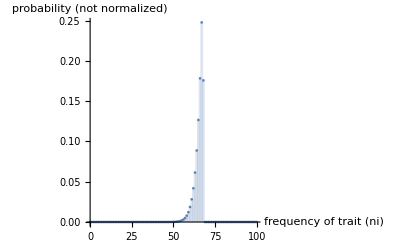

```mathematica
l=1000; t = 100; nt = 100; r = 6; b0=0.01; nc=5;
DiscretePlot[{traitAbundDist [l,t,nt,nc,b0,r,ni]/
Sum[traitAbundDist [l,t,nt,nc,b0,r,ndum],{ndum,0,nt}]} ,
{ni,0,100}, PlotRange->Full, AxesLabel->{"frequency of trait (ni)","probability (not normalized)"}]
Clear[l,t,nt,r,b0,nc]
```

If r is very small (specifically in the smaller than 1 regime) the results stop making sense because we encounter situations where the focal individual is surrounded by individuals who all have the trait but the average r is less than 1 (which doesn't make sense). I think I should model average repertoire size as a function of other things to be able to solve this problem

### Simplifying trait distribution (not resolved)

```mathematica
FullSimplify[
Series[traitAbundDist [l,t,nt,nc,b0,r,ni],{b0,0,2}],
{nt>0, ni>0,nc>0}]//Normal
```

(b0 nc nt ((-1+nc)/(nc nt r^2))^ni r^2 Gamma[ni+nt/(-1+nc)])/(ni t Gamma[nt/(-1+nc)])+(b0^2 nc nt ((-1+nc)/(nc nt r^2))^ni r^2 Gamma[ni+nt/(-1+nc)] (1-ni+nc nt r^2 (HarmonicNumber[nt/(-1+nc)]+PolyGamma[0,ni]-PolyGamma[0,ni+nt/(-1+nc)])))/(ni t^2 Gamma[nt/(-1+nc)])

```mathematica
Manipulate[
DiscretePlot[{(*traitAbundDist [l,t,nt,nc,b0,r,ni]/Sum[traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}],*)
(b0 nc nt ((-1+nc)/(nc nt r^2))^ni r^2 Gamma[ni+nt/(-1+nc)])/(ni t Gamma[nt/(-1+nc)])/Sum[traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}],
(b0 nc nt ((-1+nc)/(nc nt r^2))^ni r^2 Gamma[ni+nt/(-1+nc)])/(ni t Gamma[nt/(-1+nc)])+(b0^2 nc nt ((-1+nc)/(nc nt r^2))^ni r^2 Gamma[ni+nt/(-1+nc)] (1-ni+nc nt r^2 (HarmonicNumber[nt/(-1+nc)]+PolyGamma[0,ni]-PolyGamma[0,ni+nt/(-1+nc)])))/(ni t^2 Gamma[nt/(-1+nc)])/Sum[traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}]},
{ni,0,100}, PlotRange->Full, AxesLabel->{"frequency of trait (ni)","probability (not normalized)"}],
{{l,100},1,1000},{{t,100},1,1000},{{nt,500},1,1000},{{r,2},0,10},{{b0,0.01},0,1},{{nc,3},1,40}]
```

### Average number of repertoire size of an individual (given an external repertoire size)

t: number of traits
l: number of rounds of learning
ra: average asocial repertoire
rs: average social repertoire

```mathematica
ra = t(1-(1-b0/t)^l)
```

(1-(1-b0/t)^l) t

```mathematica
Limit[ra,t->Infinity]
```

b0 l

```mathematica
Series [ra,{b0,0,1}]//Normal
```

b0 l

```mathematica
rs = t(1-(1-(q (1+(-1+nc) q))/(nc r^2))^l) /. q -> ni/nt
```

(1-(1-(ni (1+((-1+nc) ni)/nt))/(nc nt r^2))^l) t

```mathematica
(*It would be interestin to think about a case where the number of possible traits is infinity and a trait won't be gained by innovation twice*)
```

```mathematica
Clear[indivRepertoire];
indivRepertoire [l_,t_,nt_,nc_,b0_,r_]:= IndivRepertoire [l,t,nt,nc,b0,r] = (*why is this so slow compared to just writing the equations?*)
Sum[( traitAbundDist [l,t,nt,nc,b0,r,ni]/ Sum[ traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}]) (1-(1-(ni (1+((-1+nc) ni)/nt))/(nc nt r^2))^l)  t, {ni,0,nt}]
```

```mathematica
Sum[( traitAbundDist [l,t,nt,nc,b0,r,ni]/ Sum[ traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}]) (1-(1-(ni (1+((-1+nc) ni)/nt))/(nc nt r^2))^l)  t, {ni,0,nt}]/.{l->13, t -> 100, nt -> 50, r -> 3, b0->0.1, nc->5}
```

0.0320499+0. ⅈ

The effect of different parameters on the average repertoire size is investigated by manipulate plots which are in file (“CulturalEvolution_NetworkBasics_manipulate.nb”)

### population repertoire size

```mathematica
Clear[popRepertoire];
popRepertoire [l_,t_,nt_,nc_,b0_]:= popRepertoire[l,t,nt,nc,b0]=

(*If[z=*)r/. FindRoot[r==b0 l (*asocial repertoire*)+ Sum[ ( traitAbundDist [l,t,nt,nc,b0,r,ni]/ Sum[ traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}]) (1-(1-(ni (1+((-1+nc) ni)/nt))/(nc nt r^2))^l)  t, {ni,0,nt}],{r,0.8,10}, Method->"Brent"]
(*;
Length[z]>0,z,{-1}]//Quiet *)
```

```mathematica
popRepertoire[20,100,110,5,0.2]
```

4.99458

```mathematica
Manipulate[DiscretePlot[ 
popRepertoire[l,t,nt,nc,b0],
{l,3,20}, PlotRange-> Full, AxesLabel->{"average repertoire size (r)","(average social repertoire(rs))"}],
 {nt,100}, {t,1000},{nc,5},{b0,.2}]
```

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

ReplaceAll::reps: {FindRoot[r==0.2 1+∑_(ni=0)^100 (traitAbundDist[«7»] Power[«2»]) (1+Times[«2»]) 1000,{r,0.8,10},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

ReplaceAll::reps: {FindRoot[r==0.2 1+∑_(ni=0)^100 (traitAbundDist[«7»] Power[«2»]) (1+Times[«2»]) 1000,{r,0.8,10},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
DiscretePlot[ 
popRepertoire[l,t,nt,nc,b0]/.{nt->100,t->100,nc->5,b0->0.2},
{l,10,20}, PlotRange-> Full, AxesLabel->{"average repertoire size (r)","(average social repertoire(rs))"}]
```

$Aborted

### Mean and variance of trait abundance

```mathematica
meanTraitAbund= FullSimplify[Sum[ni/nt traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}],{nt>1,l>1,t>1,nc>1,b0>0,r>1}]
```

(b0 nc nt r^2 [1+nt])/(b0-b0 nc-t+nc t)

```mathematica
varTraitAbund = Sum[(ni/nt)^2 traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}]-Sum[ni/nt traitAbundDist [l,t,nt,nc,b0,r,ni],{ni,0,nt}]^2
```

-(b0^2 nc^2 nt^2 r^4 [1+nt]^2)/((-1+nc)^2 (b0-t)^2)-(b0 nc r^2 [1+nt])/((-1+nc) (b0-t))